{0,1.×10^-6,1.36747×10^-6,1.86997×10^-6,2.55713×10^-6,3.4968×10^-6,4.78176×10^-6,6.53891×10^-6,8.94176×10^-6,0.0000122276,0.0000167209,0.0000228653,0.0000312675,0.0000427574,0.0000584694,0.0000799551,0.000109336,0.000149514,0.000204456,0.000279587,0.000382327,0.00052282,0.00071494,0.000977659,0.00133692,0.00182819,0.0025,0.00341867}

{{5.×10^-7,7.8422×10^-7},{1.18373×10^-6,2.02498×10^-6},{1.61872×10^-6,2.66137×10^-6},{2.21355×10^-6,3.64834×10^-6},{3.02696×10^-6,4.82678×10^-6},{4.13928×10^-6,6.81273×10^-6},{5.66034×10^-6,8.42063×10^-6},{7.74034×10^-6,0.0000127396},{0.0000105847,0.0000168089},{0.0000144742,0.000023831},{0.0000197931,0.0000320968},{0.0000270664,0.0000444364},{0.0000370125,0.0000590663},{0.0000506134,0.0000755994},{0.0000692123,0.00010216},{0.0000946457,0.000143396},{0.000129425,0.000187529},{0.000176985,0.00026557},{0.000242021,0.00034796},{0.000330957,0.000469842},{0.000452573,0.000598371},{0.00061888,0.000783599},{0.000846299,0.00104694},{0.00115729,0.00124298},{0.00158256,0.00139014},{0.0021641,0.00156336},{0.00295934,1.6122×10^-6}}

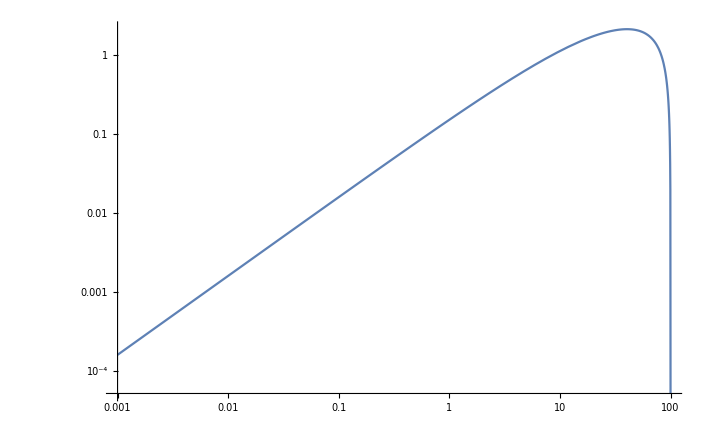

```mathematica
SetDirectory[NotebookDirectory[]];
tab=Import["specout4e","TSV"];
tab=Flatten[tab,1]//ToExpression(*Imports list of photon energies for nevents in TeV*);
nevents=10000;
DPmass=5. 10^-3;(*Mediator Mass in TeV*)
bincount=25;
minbin=10.^-6;
maxbin=0.5DPmass;(*Basically this is your DM mass in TeV*)
dlogE=(Log10[maxbin]-Log10[minbin])/bincount;
bins=Append[Prepend[Table[10^li,{li,Log10[minbin],Log10[maxbin],dlogE}],0],10^(Log10[maxbin]+dlogE)]
f[in_]:=Table[in>bins[[i]],{i,1,Length[bins]}];
tabsplit=SplitBy[tab,f[#]&];
en[j_]:=(bins⟦j⟧+bins⟦j+1⟧)/2(*Mean[tabsplit⟦j⟧]*);
dE[j_]:=bins⟦j+1⟧-bins⟦j⟧;
EdN[j_]:=Sum[tabsplit[[j,i]],{i,1,Length[tabsplit⟦j⟧]}];
binnedtab=Table[{en[j],1/nevents en[j] EdN[j]/dE[j]},{j,1,Length[tabsplit]}]
binnedtab=Drop[binnedtab,1];
dNdx0[x0_,ϵf_]:=(1/137.)/π(1+(1-x0)^2)/x0(Log[(4(1-x0))/ϵf^2]-1);(*Photon spectrum for one mediator decaying at rest to e^+e^-γ*)
dNdE0[E0_,mA_]:=2/mA dNdx0[2 E0/mA,2(0.511 10^-6)/mA];
E2dNdE0[E0_,mA_]:=E0^2 dNdE0[E0,mA];
dNdx1[x1_,ϵ1_,ϵf_]:=(t1max=Min[1,(2x1)/ϵ1^2(1+√(1-ϵ1^2))];
t1min=(2x1)/ϵ1^2(1-√(1-ϵ1^2));
2NIntegrate[1/(x0 √(1-ϵ1^2))dNdx0[x0,ϵf],{x0,t1min,t1max}])(*boosted photon spectrum from two mediators*)
dNdE1e[En_,mχ_,mA_]:=1/mχ dNdx1[En/mχ,(2mA)/mχ,(2*0.511 10^-6(*TeV*))/mA]
(*ListLogLogPlot[binnedtab,PlotStyle-> {Blue,Green},PlotRange-> All(*{{minbin,maxbin},{0.00001,0.001}}*)];
Show[%,LogLogPlot[2(*2 since two mediators per annihilation*)E2dNdE0[En,DPmass],{En,minbin,maxbin},PlotRange->All(*{{minbin,maxbin},{0.00001,0.001}}*)]]
*)

LogLogPlot[En^2 dNdE1e[En,100.,5. 10^-3],{En,0.001,100.-0.002},PlotRange->All]
(*binnedoveranalytic=Table[{binnedtab⟦i,1⟧,binnedtab⟦i,2⟧/(2E2dNdE0[binnedtab⟦i,1⟧,DPmass])},{i,1,Length[binnedtab]}];
ListLogLogPlot[binnedoveranalytic,PlotRange-> All(*{{minbin,maxbin*1.1},{1.,10.}}*)]*)
```

{0,1.×10^-6,1.36747×10^-6,1.86997×10^-6,2.55713×10^-6,3.4968×10^-6,4.78176×10^-6,6.53891×10^-6,8.94176×10^-6,0.0000122276,0.0000167209,0.0000228653,0.0000312675,0.0000427574,0.0000584694,0.0000799551,0.000109336,0.000149514,0.000204456,0.000279587,0.000382327,0.00052282,0.00071494,0.000977659,0.00133692,0.00182819,0.0025,0.00341867}

1

0.5

0.08129

0.0829895

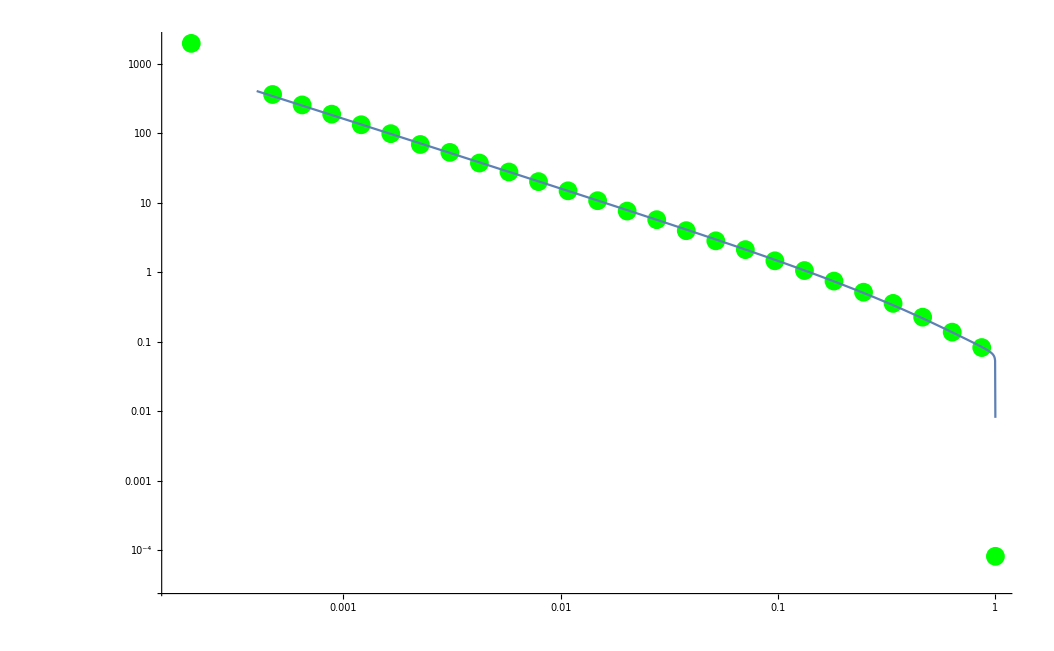

```mathematica
SetDirectory[NotebookDirectory[]];
tab=Import["pythonoutput","TSV"];
tab=Flatten[tab,1]//ToExpression(*Imports list of photon energies for nevents in TeV*);
nevents=200000;
DPmass=5. 10^-3;(*Mediator Mass in TeV*)
bincount=25;
minbin=10.^-6;
maxbin=0.5DPmass;(*Basically this is your DM mass in TeV*)
dlogE=(Log10[maxbin]-Log10[minbin])/bincount;
bins=Append[Prepend[Table[10^li,{li,Log10[minbin],Log10[maxbin],dlogE}],0],10^(Log10[maxbin]+dlogE)]
f[in_]:=Table[in>bins[[i]],{i,1,Length[bins]}];
tabsplit=SplitBy[tab,f[#]&];
dN[j_]:=Length[tabsplit⟦j⟧]
dE[j_]:=bins⟦j+1⟧-bins⟦j⟧;
en[j_]:=(bins⟦j⟧+bins⟦j+1⟧)/2;
dNdE0p[j_]:=1/nevents dN[j]/dE[j];
dNdx0p[j_,mA_]:=mA/2 dNdE0p[j];
dNdE0tab=Table[{(Min[tabsplit⟦j⟧]+Max[tabsplit⟦j⟧])/2,dNdE0p[j]},{j,1,Length[tabsplit]}];
dNdx0tab=Table[{2((Min[tabsplit⟦j⟧]+Max[tabsplit⟦j⟧])/2)/DPmass,dNdx0p[j,DPmass]},{j,1,Length[tabsplit]}];
x1t=50./100.;
ϵ1t=2 DPmass/100.;
t1max=Min[1,(2x1t)/ϵ1t^2(1+√(1-ϵ1t^2))]
t1min=(2x1t)/ϵ1t^2(1-√(1-ϵ1t^2))
tabint=Select[tab,DPmass/2 t1max>#>DPmass/2 t1min&];
tabint=1/nevents Table[1/(2tabint⟦i⟧/DPmass),{i,1,Length[tabint]}];
Sum[tabint⟦i⟧,{i,1,Length[tabint]}]

dNdx1p[E1_,mχ_,mA_]:=(
x1p=E1/mχ;(*No 2 here as we are boosting, but not decaying into two products*)
ϵ1p=2 mA/mχ;
t1maxp=Min[1,(2x1p)/ϵ1p^2(1+√(1-ϵ1p^2))];
t1minp=(2x1p)/ϵ1p^2(1-√(1-ϵ1p^2));
tabintp=Select[tab,mA/2 t1maxp>#>mA/2 t1minp&];
tabintp=1/nevents Table[1/(2tabintp⟦i⟧/mA),{i,1,Length[tabintp]}];
Sum[tabintp⟦i⟧,{i,1,Length[tabintp]}]
)

dNdx1[x1t,ϵ1t,(2*0.511 10^-6(*TeV*))/DPmass]

dNdx0[x0_,ϵf_]:=(1/137.)/π(1+(1-x0)^2)/x0(Log[(4(1-x0))/ϵf^2]-1);(*Photon spectrum for one mediator decaying at rest to e^+e^-γ*)
dNdE0[E0_,mA_]:=2/mA dNdx0[2 E0/mA,2(0.511 10^-6)/mA];
E2dNdE0[E0_,mA_]:=E0^2 dNdE0[E0,mA];
dNdx1[x1_,ϵ1_,ϵf_]:=(t1max=Min[1,(2x1)/ϵ1^2(1+√(1-ϵ1^2))];
t1min=(2x1)/ϵ1^2(1-√(1-ϵ1^2));
2NIntegrate[1/(x0 √(1-ϵ1^2))dNdx0[x0,ϵf],{x0,t1min,t1max}])(*boosted photon spectrum from two mediators*)
dNdE1e[En_,mχ_,mA_]:=1/mχ dNdx1[En/mχ,(2mA)/mχ,(2*0.511 10^-6(*TeV*))/mA]

ListLogLogPlot[dNdx0tab,PlotStyle-> {Blue,Green},PlotRange-> All(*{{minbin,maxbin},{0.00001,0.001}}*)];
Show[%,LogLogPlot[2(*2 since two mediators per annihilation*)dNdx0[x0,2 (0.511 10^-6)/DPmass],{x0,2 minbin/DPmass,2 maxbin/DPmass}(*{En,minbin,maxbin}*),PlotRange->All]]
```

{{1.5,21.6828},{11.35,124.106},{21.2,182.967},{31.05,214.631},{40.9,214.538},{50.75,203.205},{60.6,177.189},{70.45,152.013},{80.3,107.565},{90.15,55.1712},{100.,0.}}

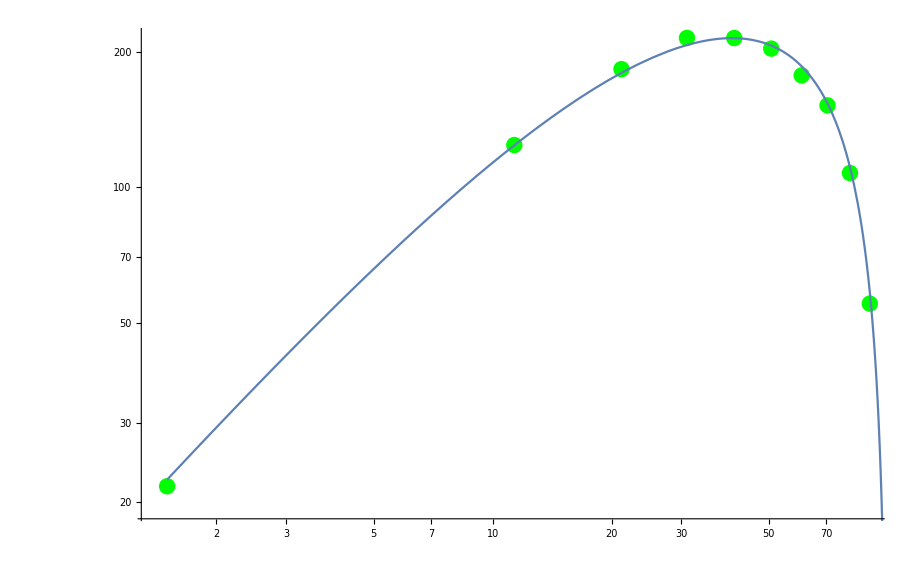

```mathematica
dNdx1p[E1_,mχ_,mA_]:=(
x1p=E1/mχ;(*No 2 here as we are boosting, but not decaying into two products*)
ϵ1p=2 mA/mχ;
t1maxp=Min[1,(2x1p)/ϵ1p^2(1+√(1-ϵ1p^2))];
t1minp=(2x1p)/ϵ1p^2(1-√(1-ϵ1p^2));
tabintp=Select[tab,mA/2 t1maxp>#>mA/2 t1minp&];
tabintp=1/nevents Table[1/(2tabintp⟦i⟧/mA),{i,1,Length[tabintp]}];
Sum[tabintp⟦i⟧,{i,1,Length[tabintp]}]
)

DPmass=5. 10^-3;
MDM=100.;
Table[{En,En^2 dNdx1p[En,MDM,DPmass]},{En,1.5,MDM,(MDM-1.5)/10.}]
ListLogLogPlot[%,PlotStyle->Green];
Show[%,LogLogPlot[En^2 dNdx1[En/MDM,2 DPmass/MDM,(2*0.511 10^-6(*TeV*))/DPmass],{En,1.5,MDM}]]
```

```mathematica
AbsoluteTiming[dNdx1p[50.,100.,5 10^-3]]
dNdx1[50./100.,(5 10^-3)/100.,(2*0.511 10^-6(*TeV*))/(5. 10^-3)]
```

{0.513891,0.08129}

0.0829895